Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

alphaAngle: 1.57 , emissionAngle: 1.0472, inclinationAngle: 2.12273

1.0472

3.16845

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

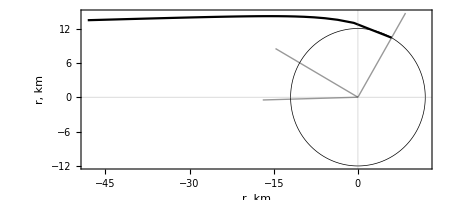

```mathematica
Clear["Global`*"]

R0:=12;
alphaAngle:=1.57;
rg:=4.134
emissionAngle:=Pi/2-Pi/6.;

b:=R0 Sin[alphaAngle]/Sqrt[1-rg/R0]

positiveDirection=True;
trajectoryPsi=θ/.Solve[b^2/r^2==1-Cos[θ-inclinationAngle-emissionAngle]^2+(1-Cos[θ-inclinationAngle-emissionAngle])^2 rg/r,θ][[3]];

inclinationAngle=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[2]];


Print["alphaAngle: ",alphaAngle," , emissionAngle: ",emissionAngle,", inclinationAngle: ",inclinationAngle];

Print[trajectoryPsi/.r->R0]
Print[trajectoryPsi/.r->10000]

rRange=Range[R0,50,1];
θRange=trajectoryPsi/.r->rRange/.C[1]->0;

p1=ListPolarPlot[{Transpose[{θRange,rRange}]},Joined->True,PlotTheme->"Scientific",PlotStyle->{Black,Dashed,GrayLevel[0]}];


trajectoryPsi1=θ/.Solve[b^2/r^2==1-Cos[θ-inclinationAngle1-emissionAngle]^2+(1-Cos[θ-inclinationAngle1-emissionAngle])^2 rg/r,θ][[4]];

inclinationAngle1=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[1]];

rRange1=Range[R0,50,1];
θRange1=trajectoryPsi1/.r->rRange/.C[1]->0;


p2=ListPolarPlot[{Transpose[{θRange1,rRange1}]},Joined->True,PlotTheme->"Scientific",PlotStyle->{Black,AbsoluteThickness[0.5],GrayLevel[0]}];

p3=PolarPlot[R0,{θ,0,2Pi},PlotTheme->"Scientific",PlotStyle->{Black,AbsoluteThickness[0.5],GrayLevel[0]},PolarGridLines->{{{inclinationAngle+emissionAngle,Black,GrayLevel[0]},{alphaAngle+emissionAngle,Black},{emissionAngle,Black}},{}}];

Show[p3,p1,PlotRange->30,PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[1.0]],FrameLabel->{Style["r, km",16],Style["r, km",16]}]
```

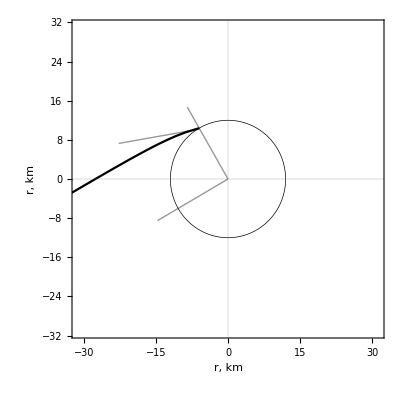

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

alphaAngle: 1.5708 , emissionAngle: 2.82743, inclinationAngle: -2.12416 , θ[0]: 2.82743 , θ[10000]: 0.704752

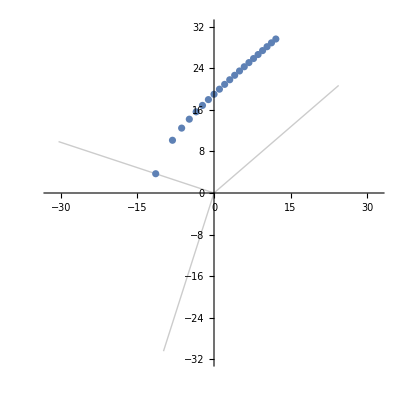

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

BSurf:=1.5*10^13;
R0:=12;
rg:=4.134;


(*Ray bending*)

alphaAngle:=Pi/2.;
emissionAngle:=Pi/2.5+Pi/2;

b:=R0 Sin[alphaAngle]/Sqrt[1-rg/R0];

positiveDirection=!True;

If[positiveDirection,
trajectoryTheta=θ/.Solve[b^2/(z+R0)^2==1-Cos[θ-inclinationAngle-emissionAngle]^2+(1-Cos[θ-inclinationAngle-emissionAngle])^2 rg/(z+R0),θ][[3]];
inclinationAngle=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[2]];

,
trajectoryTheta=θ/.Solve[b^2/(z+R0)^2==1-Cos[θ-inclinationAngle-emissionAngle]^2+(1-Cos[θ-inclinationAngle-emissionAngle])^2 rg/(z+R0),θ][[4]];
inclinationAngle=t/.Solve[1-Cos[alphaAngle]==(1-Cos[t])(1-rg/R0),t][[1]];]

Print["alphaAngle: ",alphaAngle," , emissionAngle: ",emissionAngle,", inclinationAngle: ",inclinationAngle," , θ[0]: ",trajectoryTheta/.z->0," , θ[10000]: ",trajectoryTheta/.z->10000];

(*Print[];
Print[];*)

zRange:=Range[0,20,1];
θRange:=trajectoryTheta/.z->zRange/.C[1]->0;

p0=ListPolarPlot[Transpose[{θRange,zRange+R0}],PlotRange->R0+Max[zRange],PolarGridLines->{{inclinationAngle+emissionAngle,alphaAngle+emissionAngle,emissionAngle},{}}]
```

```mathematica
1.22/(Pi/2)*90
```

69.9009